### 2.21

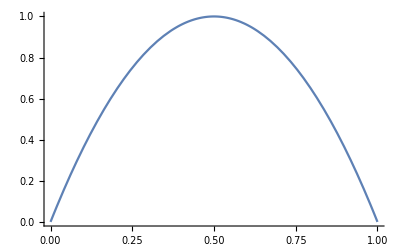

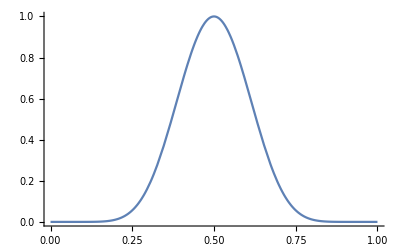

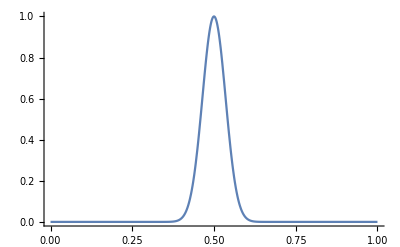

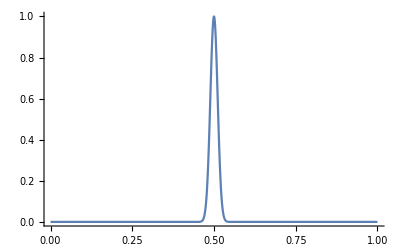

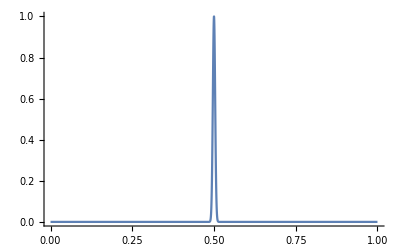

```mathematica
Ω[z_,n_]:=(4z(1-z))^n
Plot[Ω[z,1],{z,0,1},PlotRange->All]
Plot[Ω[z,10],{z,0,1},PlotRange->All]
Plot[Ω[z,100],{z,0,1},PlotRange->All]
Plot[Ω[z,1000],{z,0,1},PlotRange->All]
Plot[Ω[z,10000],{z,0,1},PlotRange->All]
```

264.421

187.529

60

40

0

100

24859.1

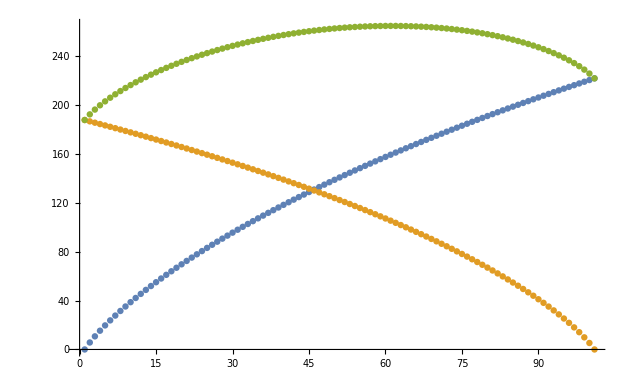

```mathematica
qa = Range[101]-1;
qb=Reverse[qa];
na=300;
nb=200;
Ωa=((qa+na-1)!)/(qa!(na-1)!);
Ωb=((qb+nb-1)!)/(qb!(nb-1)!);
sa=Log[Ωa];
sb=Log[Ωb];
stot=Log[Ωa]+Log[Ωb];
Max[stot]//N
Min[stot]//N
maxPos=Position[stot,Max[stot]]⟦1,1⟧;
minPos=Position[stot,Min[stot]]⟦1,1⟧;
qa⟦maxPos⟧
qb⟦maxPos⟧
qa⟦minPos⟧
qb⟦minPos⟧
Total[stot]//N
ListPlot[{Log[Ωa],Log[Ωb],Log[Ωa]+Log[Ωb]}]
```

```mathematica
n=10^23;
q=n;
((q+n)Log[q+n]-q Log[q]-n Log[n]//N)*1.381*2
(*Ω=Log[((q+n)^(q+n)ⅇ^(-(q+n))√(2π (q+n)))/(q^q ⅇ^-q √(2π q)n^n ⅇ^-n √(2π n))]//N*)
```

3.82895×10^23

```mathematica
n=10^23;
(4 n Log[2]-Log[√(8 π n)])*1.381//N
```

3.82895×10^23